# # TPMN Project - Tight Biding Model

```mathematica
$Assumptions = {x∈Reals, y∈Reals,θ∈Reals,ϕ∈Reals}
```

{x∈Reals,y∈Reals,θ∈Reals,ϕ∈Reals}

## In the following section we present a sumary about the Spherical Harmonics that consist in the angular part of the solution of the Schrödinger equation, while the remaining part consist in the radial contribution of the wavefunction. The study of the angular part represents an critical point in the Tight Biding Model for the contribution of the electrons in orbitals locate in differents sites of solid’s lattice.

## · Definition of range of (l,m)

```mathematica
Here we define a the range of the spherical harmonics functions that we are interested in to study.
```

```mathematica
lval = Range[0, 2];
mval= Range[-2,2];
lm =Transpose[Tuples[{lval, mval}]]
```

{{0,0,0,0,0,1,1,1,1,1,2,2,2,2,2},{-2,-1,0,1,2,-2,-1,0,1,2,-2,-1,0,1,2}}

```mathematica
l =lm[[1]];
m= lm[[2]];
```

## · Definition of Spherical Harmonics

```mathematica
We do plot the spherical harmonics functions (Y(l,m)) using the internal functions of Mathematica:
```

```mathematica
Y[x_,y_]=SphericalHarmonicY[l, m,x,y]
(*Table[SphericalPlot3D[Abs[f],{x,-Pi,Pi},{y,-4*Pi,4*Pi}, PlotRange->All]]*)
```

{0,0,1/(2 √π),0,0,0,1/2 ⅇ^(-ⅈ y) √(3/(2 π)) Sin[x],1/2 √(3/π) Cos[x],-1/2 ⅇ^(ⅈ y) √(3/(2 π)) Sin[x],0,1/4 ⅇ^(-2 ⅈ y) √(15/(2 π)) Sin[x]^2,1/2 ⅇ^(-ⅈ y) √(15/(2 π)) Cos[x] Sin[x],1/4 √(5/π) (-1+3 Cos[x]^2),-1/2 ⅇ^(ⅈ y) √(15/(2 π)) Cos[x] Sin[x],1/4 ⅇ^(2 ⅈ y) √(15/(2 π)) Sin[x]^2}

```mathematica
(*Y[l,m][[1]]*)
```

```mathematica
Table[SphericalPlot3D[Abs[SphericalHarmonicY[ll,mm,x,y]],{x,0,Pi},{y,0,2 Pi}],{ll,0,2},{mm,-2,2}]
```

{{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}}

## Building the matrix of the SH with l-th component as column (^) and the m-th component as row (->):

```mathematica
SH= Transpose[Partition[Y[x,y], 5]]
```

{{0,0,1/4 ⅇ^(-2 ⅈ y) √(15/(2 π)) Sin[x]^2},{0,1/2 ⅇ^(-ⅈ y) √(3/(2 π)) Sin[x],1/2 ⅇ^(-ⅈ y) √(15/(2 π)) Cos[x] Sin[x]},{1/(2 √π),1/2 √(3/π) Cos[x],1/4 √(5/π) (-1+3 Cos[x]^2)},{0,-1/2 ⅇ^(ⅈ y) √(3/(2 π)) Sin[x],-1/2 ⅇ^(ⅈ y) √(15/(2 π)) Cos[x] Sin[x]},{0,0,1/4 ⅇ^(2 ⅈ y) √(15/(2 π)) Sin[x]^2}}

```mathematica
Dimensions[MatrixSH];
MatrixSH=MatrixForm[SH]
```

(0 | 0 | 1/4 ⅇ^(-2 ⅈ y) √(15/(2 π)) Sin[x]^2
0 | 1/2 ⅇ^(-ⅈ y) √(3/(2 π)) Sin[x] | 1/2 ⅇ^(-ⅈ y) √(15/(2 π)) Cos[x] Sin[x]
1/(2 √π) | 1/2 √(3/π) Cos[x] | 1/4 √(5/π) (-1+3 Cos[x]^2)
0 | -1/2 ⅇ^(ⅈ y) √(3/(2 π)) Sin[x] | -1/2 ⅇ^(ⅈ y) √(15/(2 π)) Cos[x] Sin[x]
0 | 0 | 1/4 ⅇ^(2 ⅈ y) √(15/(2 π)) Sin[x]^2)

```mathematica
For example, the SH function for l=2, m=1:
```

```mathematica
SH[[3,2]]
```

1/2 √(3/π) Cos[x]

## Combination of the different SH that belongs to each state i.e (l1,m1) - (l):

```mathematica
Combinations[l1_, l2_, m1_, m2_] := Refine[Conjugate[SH][[l1, m1]] * SH[[l2, m2]]]
```

+ Example of combination between element Combinations(2,1) with Combinations(3,2):

```mathematica
SH[[2,1]]
```

0

```mathematica
Conjugate[SH][[2]]
```

{0,1/2 ⅇ^(ⅈ Conjugate[y]) √(3/(2 π)) Conjugate[Sin[x]],1/2 ⅇ^(ⅈ Conjugate[y]) √(15/(2 π)) Conjugate[Cos[x] Sin[x]]}

```mathematica
funct =Combinations[2,3,1,2]
```

0

+ Example of the integration of the previous combinations:

```mathematica
Integrate[funct, {x, 0, Pi/2}, {y, 0, Pi}]
```

0

## Plots of all the combinations of the SH:

```mathematica
Table[SphericalPlot3D[Combinations[ i, j,k,l],{x,0,2*Pi},{y,0,Pi}, PlotRange->All], {i, 1, 3}, {j, 1, 3},{k, 1,3}, {l, 1, 3}]
```

{{{{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-}},{{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-}},{{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-}}},{{{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-}},{{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-}},{{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-}}},{{{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-}},{{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-}},{{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-,-Graphics3D-}}}}

## Integrals over all combinations:

```mathematica
Table[For[q=1,q≤2,q++,For[r=1,r≤2,r++,For[s=1,s≤2,s++,For[t=1,t≤2,t++,Print[Integrate[Combinations[q,r,s,t],{x,0, Pi/2}, {y,0,Pi}] ]]]]]]
```

0

0

0

«12 more identical outputs»

(3 π)/32

```mathematica
Now,in order to use these funcitons for our main porpuse in the description of the physics of the electrons in the lattice of a solid, we have to consider that this orbital have to be locate in different sites of the lattice which means, that the contribution of each orbital due to the potential in the neighbour site are not straighforward as just to compute the on-site integral. However, the formalism of LCAO allow us to compute this contribution by considering either, the rotation of the frame of reference of the neighbour site or by considering the rotation of the orbitals in the direction of a convinient axis where the contribution is proportional to the on-site direction. In this section we are going to compute the matrix elements of the Hamiltonian corresponding to this contributions over the all dispositions of the differents orbitals:
```

## Calculation of the Hamiltonian · Preliminary definitions and calculations

Transformations from the space of Spherical Harmonics’ basis into the Orbital basis i.e T : Y_lm -> p_xi ; the transformation for the s-states it is trivial, however for the p-states {v1, v2, v3} and the d-states {b1, b2, b3, b4, b5} are not so:

```mathematica
v1 ={I/Sqrt[2],0,I/Sqrt[2]};
v2 ={0,1,0};
v3={1/Sqrt[2],0,-1/Sqrt[2]};

b1={I/Sqrt[2], 0,0,0, -I/Sqrt[2]};
b2={0,I/Sqrt[2],0,I/Sqrt[2],0};
b3={0,0,1,0,0};
b4={0,1/Sqrt[2],0,-1/Sqrt[2],0};
b5={1/Sqrt[2],0,0,0,1/Sqrt[2]};
```

Building the transformation matrices with the basis set found above for each type of orbital and the transformation T:

```mathematica
sT=1;(*//MatrixForm*)
pT={v1,v2,v3};(*//MatrixForm*)
dT={b1,b2,b3,b4,b5};(*//MatrixForm*)
```

```mathematica
T= ArrayFlatten[{{sT,0,0},{0,pT,0},{0,0,dT}}];(*//MatrixForm*)
Tdag=ConjugateTranspose[T];(*//MatrixForm*)
FullSimplify[MatrixForm[Tdag]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ/(√2) | 0 | 1/(√2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ/(√2) | 0 | -1/(√2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 1/(√2)
0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 1/(√2) | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | -1/(√2) | 0
0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 1/(√2))

Now another important transformation is related to the rotations of the orbitals in the different sites (e.g site A and B) into a positions where they can be described as a local frame. This is achieved as a rotation operators with the shape: RLy=exp{iøLy} and RLz=exp{i∑Lz}; however, we are interested in the rotations using the same basis set, for instance the Lz basis set. For this reason, we build the transformation matrix M : Ly ->Lz obtained from l=0,1,2 and m=+-l :

```mathematica
l0=0;l1=1;l2=2;

Lx11=ConstantArray[0,{2*l0+1,2*l0+1}];
Ly11=ConstantArray[0,{2*l0+1,2*l0+1}];
Lz11=ConstantArray[0,{2*l0+1,2*l0+1}];

Lx33=ConstantArray[0,{2*l1+1,2*l1+1}];
Ly33=ConstantArray[0,{2*l1+1,2*l1+1}];
Lz33=ConstantArray[0,{2*l1+1,2*l1+1}];

Lx55=ConstantArray[0,{2*l2+1,2*l2+1}];
Ly55=ConstantArray[0,{2*l2+1,2*l2+1}];
Lz55=ConstantArray[0,{2*l2+1,2*l2+1}];
```

```mathematica
Creating the Lx,Ly,Lz matrices for l=0
```

```mathematica
Lx11=1;
Ly11=1;
Lz11=1;
```

```mathematica
Creating the Lx, Ly,Lz  matrices for l=1
```

```mathematica
For[ii=1,ii<(2*l1+1),ii++, 
mval=Range[-l1,l1];
Lx33[[ii,ii+1]]= Sqrt[l1(l1+1)-(mval[[ii]]+1)mval[[ii]] ];
Lx33[[ii+1,ii]]=Sqrt[l1(l1+1)-(mval[[ii+1]]-1)mval[[ii+1]] ];
];(*//MatrixForm*)

For[ii=1,ii<(2*l1+1),ii++, 
mval=Range[-l1,l1];
Ly33[[ii,ii+1]]=Sqrt[l1(l1+1)-(mval[[ii]]+1)mval[[ii]] ];
Ly33[[ii+1,ii]]=Sqrt[l1(l1+1)-(mval[[ii+1]]-1)mval[[ii+1]] ];
];(*//MatrixForm*)

For[ii=1,ii<(2*l1+1+1),ii++, 
mval=Range[-l1,l1];
Lz33[[ii,ii]]=mval[[ii]]
];(*//MatrixForm*)
```

```mathematica
Creating the Lx, Ly,Lz  matrices for l=2
```

```mathematica
For[ii=1,ii<(2*l2+1),ii++, 
mval=Range[-l2,l2];
Lx55[[ii,ii+1]]= Sqrt[l2(l2+1)-(mval[[ii]]+1)mval[[ii]] ];
Lx55[[ii+1,ii]]=Sqrt[l2(l2+1)-(mval[[ii+1]]-1)mval[[ii+1]] ];
];(*//MatrixForm*)

For[ii=1,ii<(2*l2+1),ii++, 
mval=Range[-l2,l2];
Ly55[[ii,ii+1]]=Sqrt[l2(l2+1)-(mval[[ii]]+1)mval[[ii]] ];
Ly55[[ii+1,ii]]=Sqrt[l2(l2+1)-(mval[[ii+1]]-1)mval[[ii+1]] ];
];(*//MatrixForm*)

For[ii=1,ii<(2*l2+1+1),ii++, 
mval=Range[-l2,l2];
Lz55[[ii,ii]]=mval[[ii]]
];(*//MatrixForm*)
```

```mathematica
Creating the M matrix with the Ly11, Ly33 and Ly55 (eigenvectors of Ly) for the s-, p- and d- orbitals:
```

```mathematica
M=ArrayFlatten[{{Ly11,ConstantArray[0, {1,3}],ConstantArray[0, {1, 5}]},{ConstantArray[0, {3, 1}],Ly33,ConstantArray[0, {3, 5}]},{ConstantArray[0, {5, 1}],ConstantArray[0, {5, 3}],Ly55}}];(*//MatrixForm*)
Mdag=ConjugateTranspose[M];
```

```mathematica
FullSimplify[MatrixForm[Mdag]]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | √2 | 0 | 0 | 0 | 0 | 0 | 0
0 | √2 | 0 | √2 | 0 | 0 | 0 | 0 | 0
0 | 0 | √2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | √6 | 0 | 0
0 | 0 | 0 | 0 | 0 | √6 | 0 | √6 | 0
0 | 0 | 0 | 0 | 0 | 0 | √6 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0)

### We can consider two approaches, one is using the the Euler angles, which take into account the rotations on the basis of three angles (theta, phi and eta) known as Euler angles and the second approach that is what we are going to use here, by considering the rotation operators in the Lz basis considering the cosine directors, this approach would represent a more doable way, by only considering two angles (theta and phi). In the case of the Euler angles, the rotation is more laborious to find.

```mathematica
(*Rx={{1,0,0},{0,cos[ζ],-sin[ζ]},{0,sin[ζ],cos[ζ]}};
Ry={{cos[θ],0,sin[θ]},{0,1,0},{-sin[θ],0,cos[θ]}};
Rz={{cos[ϕ],-sin[ϕ],0},{sin[ϕ],cos[ϕ],0},{0,0,1}};*) (* These ones are the rotation matrices for the Euler rotations*)
```

```mathematica
BRLyS=ConstantArray[0,{2*l0+1,2*l0+1}];
BRLzS=ConstantArray[0,{2*l0+1,2*l0+1}];
BRLyP=ConstantArray[0,{2*l1+1,2*l1+1}];
BRLzP=ConstantArray[0,{2*l1+1,2*l1+1}];
BRLyD=ConstantArray[0,{2*l2+1,2*l2+1}];
BRLzD=ConstantArray[0,{2*l2+1,2*l2+1}];
```

```mathematica
Block of rotation matrices for s-orbitals:
```

```mathematica
For[ii=1,ii<(2*l0+1+1),ii++, 
mval=Range[-l0,l0];
BRLyS[[ii,ii]]=Exp[-ⅈ*θ*mval[[ii]]]
];(*//MatrixForm*)
For[ii=1,ii<(2*l0+1+1),ii++, 
mval=Range[-l0,l0];
BRLzS[[ii,ii]]=Exp[-ⅈ*ϕ*mval[[ii]]]
];(*//MatrixForm*)
```

```mathematica
Block of rotation matrices for p-orbitals:
```

```mathematica
For[ii=1,ii<(2*l1+1+1),ii++, 
mval=Range[-l1,11];
BRLyP[[ii,ii]]=Exp[-ⅈ*θ*mval[[ii]]]
];(*//MatrixForm*)
For[ii=1,ii<(2*l1+1+1),ii++, 
mval=Range[-l1,l1];
BRLzP[[ii,ii]]=Exp[-ⅈ*ϕ*mval[[ii]]]
];(*//MatrixForm*)
```

```mathematica
Block of rotation matrices for d-orbitals:
```

```mathematica
For[ii=1,ii<(2*l2+1+1),ii++, 
mval=Range[-l2,l2];
BRLyD[[ii,ii]]=Exp[-ⅈ*θ*mval[[ii]]]
];(*//MatrixForm*)
For[ii=1,ii<(2*l2+1+1),ii++, 
mval=Range[-l2,l2];
BRLzD[[ii,ii]]=Exp[-ⅈ*ϕ*mval[[ii]]]
];(*//MatrixForm*)
```

```mathematica
However, these rotation matrices must be extended to not only s, p or d orbitals but for the spaces of them. In this sense, we build the block diagonal matrix of the rotational matrix of each orbital state:
```

```mathematica
RLy=ArrayFlatten[{{1,0,0},{0,BRLyP,0},{0,0,BRLyD}}];
RLz=ArrayFlatten[{{1,0,0},{0,BRLzP,0},{0,0,BRLzD}}];
```

```mathematica
MatrixForm[RLy]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅇ^(ⅈ θ) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(-ⅈ θ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅇ^(2 ⅈ θ) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ θ) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ θ) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-2 ⅈ θ))

```mathematica
MatrixForm[RLz]
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | ⅇ^(ⅈ ϕ) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅇ^(-ⅈ ϕ) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅇ^(2 ⅈ ϕ) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅇ^(ⅈ ϕ) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-ⅈ ϕ) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-2 ⅈ ϕ))

Then using the cannonical basis of R^9 for stablish the basis set of the s-, p- and d- states:

```mathematica
Orb=List[s={1,0,0,0,0,0,0,0,0}(*//MatrixForm*),
py={0,1,0,0,0,0,0,0,0}(*//MatrixForm*),
pz={0,0,1,0,0,0,0,0,0}(*//MatrixForm*),
px={0,0,0,1,0,0,0,0,0}(*//MatrixForm*),
dxy={0,0,0,0,1,0,0,0,0}(*//MatrixForm*),
dyz={0,0,0,0,0,1,0,0,0}(*//MatrixForm*),
dzz={0,0,0,0,0,0,1,0,0}(*//MatrixForm*),
dxz={0,0,0,0,0,0,0,1,0}(*//MatrixForm*),
dx2y2={0,0,0,0,0,0,0,0,1}(*//MatrixForm*)];
```

```mathematica
The Slater-Kaster matrix it is given by:
```

```mathematica
K={{ssσ,0,-spσ,0,0,0,sdσ,0,0},{0,ppπ,0,0,0,-pdπ,0,0,0},{spσ,0,ppσ,0,0,0,pdσ,0,0},{0,0,0,ppπ,0,0,0,-pdπ,0},{0,0,0,0,ddδ,0,0,0,0},{0,pdπ,0,0,0,ddπ,0,0,0},{sdσ,0,pdσ,0,0,0,ddσ,0,0},{0,0,0,pdπ,0,0,0,ddπ,0},{0,0,0,0,0,0,0,0,ddδ}};(*//MatrixForm*)
```

```mathematica
MatrixForm[K]
```

(ssσ | 0 | -spσ | 0 | 0 | 0 | sdσ | 0 | 0
0 | ppπ | 0 | 0 | 0 | -pdπ | 0 | 0 | 0
spσ | 0 | ppσ | 0 | 0 | 0 | pdσ | 0 | 0
0 | 0 | 0 | ppπ | 0 | 0 | 0 | -pdπ | 0
0 | 0 | 0 | 0 | ddδ | 0 | 0 | 0 | 0
0 | pdπ | 0 | 0 | 0 | ddπ | 0 | 0 | 0
sdσ | 0 | pdσ | 0 | 0 | 0 | ddσ | 0 | 0
0 | 0 | 0 | pdπ | 0 | 0 | 0 | ddπ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ddδ)

```mathematica
ssσ=-0.07835;spσ=0.11192;sdσ=-0.06197;ppσ=0.18677;ppπ=-0.02465;pdσ=-0.08564;pdπ= 0.02446; ddσ=-0.06856;ddπ=0.03528;ddδ=-0.00588;
```

```mathematica
Then, previously to compute the complete Hamiltonian, we compute the Q-miltonian:
```

```mathematica
Q= Refine[ConjugateTranspose[RLz].M.ConjugateTranspose[RLy].Mdag.Tdag.K.T.Mdag.RLy.M.RLz];(*//MatrixForm*)
```

```mathematica
FullSimplify[MatrixForm[Q]]
```

(ssσ | 0 | -4 spσ Cos[θ] | 0 | 2 √6 ⅇ^(ⅈ (θ+2 ϕ)) sdσ | 0 | 12 sdσ Cos[θ] | 0 | 2 √6 ⅇ^(-ⅈ (θ+2 ϕ)) sdσ
0 | 8 ppπ | 0 | 8 ⅇ^(-2 ⅈ ϕ) ppπ | 0 | -8 (3+ⅇ^(2 ⅈ θ)) pdπ | 0 | -8 ⅇ^(-2 ⅈ (θ+ϕ)) (1+3 ⅇ^(2 ⅈ θ)) pdπ | 0
4 spσ Cos[θ] | 0 | 16 ppσ Cos[θ]^2 | 0 | 4 √6 ⅇ^(2 ⅈ ϕ) (1+ⅇ^(2 ⅈ θ)) pdσ | 0 | 48 pdσ Cos[θ]^2 | 0 | 4 √6 ⅇ^(-2 ⅈ (θ+ϕ)) (1+ⅇ^(2 ⅈ θ)) pdσ
0 | 8 ⅇ^(2 ⅈ ϕ) ppπ | 0 | 8 ppπ | 0 | -8 ⅇ^(2 ⅈ ϕ) (3+ⅇ^(2 ⅈ θ)) pdπ | 0 | 8 (-3-ⅇ^(-2 ⅈ θ)) pdπ | 0
2 √6 ⅇ^(-ⅈ (θ+2 ϕ)) sdσ | 0 | 4 √6 ⅇ^(-2 ⅈ (θ+ϕ)) (1+ⅇ^(2 ⅈ θ)) pdσ | 0 | 8 (2 ddδ+3 ddσ) | 0 | 4 √6 ⅇ^(-2 ⅈ (θ+ϕ)) (3 ddσ+(2 ddδ+3 ddσ) ⅇ^(2 ⅈ θ)) | 0 | 24 ddσ ⅇ^(-2 ⅈ (θ+2 ϕ))
0 | 8 (3+ⅇ^(-2 ⅈ θ)) pdπ | 0 | 8 ⅇ^(-2 ⅈ (θ+ϕ)) (1+3 ⅇ^(2 ⅈ θ)) pdπ | 0 | 8 ddπ (11+6 Cos[2 θ]) | 0 | 24 ddπ ⅇ^(-2 ⅈ (θ+ϕ)) (2+3 ⅇ^(2 ⅈ θ)) | 0
12 sdσ Cos[θ] | 0 | 48 pdσ Cos[θ]^2 | 0 | 4 √6 ⅇ^(2 ⅈ ϕ) (2 ddδ+3 ddσ (1+ⅇ^(2 ⅈ θ))) | 0 | 24 (2 ddδ+3 ddσ+3 ddσ Cos[2 θ]) | 0 | 4 √6 ⅇ^(-2 ⅈ (θ+ϕ)) (3 ddσ+(2 ddδ+3 ddσ) ⅇ^(2 ⅈ θ))
0 | 8 ⅇ^(2 ⅈ ϕ) (3+ⅇ^(2 ⅈ θ)) pdπ | 0 | 8 (3+ⅇ^(2 ⅈ θ)) pdπ | 0 | 24 ddπ ⅇ^(2 ⅈ ϕ) (3+2 ⅇ^(2 ⅈ θ)) | 0 | 8 ddπ (11+6 Cos[2 θ]) | 0
2 √6 ⅇ^(ⅈ (θ+2 ϕ)) sdσ | 0 | 4 √6 ⅇ^(2 ⅈ ϕ) (1+ⅇ^(2 ⅈ θ)) pdσ | 0 | 24 ddσ ⅇ^(2 ⅈ (θ+2 ϕ)) | 0 | 4 √6 ⅇ^(2 ⅈ ϕ) (2 ddδ+3 ddσ (1+ⅇ^(2 ⅈ θ))) | 0 | 8 (2 ddδ+3 ddσ))

In order to define the nearest neighbors ,we need to determine the number of nearest neighbors which in our case the Platinum has fcc crystialline structure wich coordinate number is 12. Then the vertex (atoms) is given by the following:

```mathematica
vertex={{0.5,0.5,0},{0.5,0,0.5},{0,0.5,0.5},{-0.5,0.5,0},{-0.5,0,0.5},{0.5,-0.5,0},{0,-0.5,-0.5},{-0.5,-0.5,0},{0.5,0,-0.5},{0,0.5,-0.5},{-0.5,0,-0.5},{0,-0.5,0.5}};
ListPointPlot3D[vertex,PlotStyle->{PointSize[0.05],Black}](*Cartesian coordinates*)

(*vertex={{1,0,0},{-1, 0,0},{0,1,0},{0,-1,0},{0,0,1},{0,0,-1},{0,1,-1},{0,-1,1},{-1 ,0,1},{1,0,-1},{1,-1,0},{-1 ,1,0}}
ListPointPlot3D[vertex,PlotStyle->{PointSize[0.05],Black}]; Tetrahedral coordinates*)
(*vertex={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{-1,0,0},{0,-1,0},{0,0,-1},{0.5,0.5,0.5},{0.5,0.5,-0.5},{0.5,-0.5,0.5},{-0.5,0.5,0.5},{-0.5,-0.5,0.5},{0.5,-0.5,-0.5},{-0.5,0.5,-0.5},{-0.5,-0.5,-0.5}};
ListPointPlot3D[vertex,PlotStyle->{PointSize[0.05],Black}]*)(*Cartesian coordinates*)

ffcImage=LatticeData["FaceCenteredCubic","Image"]

ffcBasis=LatticeData["FaceCenteredCubic","Basis"];
```

-Graphics3D-

-Graphics3D-

And the Hamiltonian is defined for the general LCAO method as an empty matrix 9x9:

```mathematica
(*Clear[Hamiltonian]*) (*<-- use this in case 2nd, 3rd... run*)
Hamiltonian = ConstantArray[0, {9,9}];
```

Some tiny bug fix about the indetermination of 1/0 for:

```mathematica
Unprotect[Power];
Power[0,-1]=DirectedInfinity[1];
```

Defining the angles (theta and phi) for each near neighbour given by the vertex list and the distance between neighbours (which is constant) and the wavevector in the :

```mathematica
ph = ArcCos[Transpose[vertex][[3]]*Sqrt[2] ];
th= ArcTan[Transpose[vertex][[2]]/Transpose[vertex ][[1]] ];
Rjo = ConstantArray[1/Sqrt[2],12];
```

Building the Hamiltonian in terms of the elements of Q-Hamiltonian which means summing over the elements (i,j) and over the nearest neighbours (vertex) values of the wavevector along the directions of the points symmetry. First of all, we need to set those symmetry points:

```mathematica
(* Path along the BZ symmetry points ordered as [G, X, L, W, U, K]*)
sympoints={{0,0,0},{0,0.5,0.5},{0.5,0.5,0.5},{1/4,3/4,1/2},{1/4,5/8,5/8},{3/4,3/8,3/4}};
```

Now that we have the symmetry points in the Brillouin zone, then we can construct certains paths where we can consider the different values for the wave vector on each path:

```mathematica
kGX=(sympoints[[2]]-sympoints[[1]]);
kXW=(sympoints[[4]]-sympoints[[2]]);
kWL=(sympoints[[3]]-sympoints[[4]]);
kLG=(sympoints[[1]]-sympoints[[3]]);
kGK=(sympoints[[6]]-sympoints[[1]]);
```

```mathematica
For[i=1, i<10, i++,
For[j=1, j<10, j++,
For[vv=1, vv<13, vv++,
vecR=Rjo[[vv]]*{(Sin[th[[vv]]])*(Cos[ph[[vv]]]), (Sin[th[[vv]]])*(Sin[ph[[vv]]]), (Cos[th[[vv]]])};
Hamiltonian[[i,j]] = Hamiltonian[[i,j]]+  Exp[ⅈ*(Ktest.vecR)]*Q[[i,j]]/.{θ->th[[vv]], ϕ->ph[[vv]]}]]]
```

The matrix form of the Hamiltonian (uncomment for see):

```mathematica
FullSimplify[MatrixForm[Hamiltonian]]
```

((-0.07835+0. ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})-(0.07835+0. ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})-(0.1567+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})-(0.3134+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})-(0.1567+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})-(0.07835+0. ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(0.07835+0. ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (0.+0. ⅈ)-(0.633115+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})-(1.79072+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})-(0.633115+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5}) | 0.+0. ⅈ | (-0.30359+1.85895×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})-(0.30359-5.57685×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})+(0.429341-0.429341 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(7.4358×10^-17+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})+(0.429341+0.429341 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})+(0.30359-5.57685×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})+(0.30359-1.85895×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (0.+0. ⅈ)-(1.05167+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})-(2.97456+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})-(1.05167+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5}) | 0.+0. ⅈ | (-0.30359-1.85895×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})-(0.30359+5.57685×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})+(0.429341+0.429341 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(7.4358×10^-17+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})+(0.429341-0.429341 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})+(0.30359+5.57685×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})+(0.30359+1.85895×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0})
0.+0. ⅈ | (-0.1972+1.38778×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})-(0.1972-1.38778×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})-(0.3944+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})-(0.7888-5.55112×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})-(0.3944+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})-(0.1972-1.38778×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(0.1972-1.38778×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (0.+0. ⅈ)-(1.38778×10^-17-0.1972 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})+(1.38778×10^-17-0.1972 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})+(0.3944+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(0.3944+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})+(1.38778×10^-17-0.1972 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(1.38778×10^-17-0.1972 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (-0.39136-2.77556×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})-(0.39136+2.77556×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})-(1.17408-0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})-(3.13088-2.22045×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})-(1.17408+0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})-(0.39136+2.77556×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(0.39136+2.77556×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (0.+0. ⅈ)-(8.32667×10^-17-0.39136 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})+(8.32667×10^-17-0.39136 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})+(1.17408+0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(1.17408-0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})+(8.32667×10^-17-0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(8.32667×10^-17-0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ
(0.+0. ⅈ)+(0.633115+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(1.79072+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})+(0.633115+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5}) | 0.+0. ⅈ | (0.+0. ⅈ)+(2.98832+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(11.9533+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})+(2.98832+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5}) | 0.+0. ⅈ | (0.+0. ⅈ)+(1.67819-1.67819 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(4.11039×10^-16+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})+(1.67819+1.67819 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5}) | 0.+0. ⅈ | (0.+0. ⅈ)-(4.11072+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})-(16.4429+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})-(4.11072+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5}) | 0.+0. ⅈ | (0.+0. ⅈ)+(1.67819+1.67819 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(4.11039×10^-16+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})+(1.67819-1.67819 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})
0.+0. ⅈ | (0.+0. ⅈ)-(1.38778×10^-17+0.1972 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})+(1.38778×10^-17+0.1972 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})+(0.3944+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(0.3944+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})+(1.38778×10^-17+0.1972 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(1.38778×10^-17+0.1972 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (-0.1972-1.38778×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})-(0.1972+1.38778×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})-(0.3944+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})-(0.7888+5.55112×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})-(0.3944+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})-(0.1972+1.38778×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(0.1972+1.38778×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (0.+0. ⅈ)-(8.32667×10^-17+0.39136 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})+(8.32667×10^-17+0.39136 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})+(1.17408-0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(1.17408+0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})+(8.32667×10^-17+0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(8.32667×10^-17+0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (-0.39136+2.77556×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})-(0.39136-2.77556×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})-(1.17408+0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})-(3.13088+2.22045×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})-(1.17408-0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})-(0.39136-2.77556×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(0.39136-2.77556×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ
(-0.30359+0. ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})-(0.30359+7.4358×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})+(0.429341+0.429341 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(7.4358×10^-17+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})+(0.429341-0.429341 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})+(0.30359+3.7179×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})+(0.30359+3.7179×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (0.+0. ⅈ)+(1.67819+1.67819 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(4.11039×10^-16+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})+(1.67819-1.67819 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5}) | 0.+0. ⅈ | (-1.73952+1.06515×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})-(1.73952+1.06515×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})-(3.47904+4.44089×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})-(6.95808+2.46519×10^-32 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})-(3.47904+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})-(1.73952-1.06515×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(1.73952+1.06515×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (0.+0.115224 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})+(2.82217×10^-17-0.115224 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})+(4.26094+4.03049 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(1.01541×10^-15+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})+(4.26094-4.03049 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})+(1.41109×10^-17-0.115224 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(1.41109×10^-17-0.115224 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (-1.64544-1.00754×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})-(1.64544+7.05279×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})-(0.+3.29088 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(6.58176+1.61207×10^-15 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})-(6.66134×10^-16-3.29088 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})-(1.64544+5.03771×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(1.64544+3.02262×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0})
0.+0. ⅈ | (0.39136+2.77556×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})+(0.39136-5.55112×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})+(1.17408+0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(3.13088+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})+(1.17408-0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})+(0.39136+2.77556×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})+(0.39136-5.55112×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (0.+0. ⅈ)+(1.11022×10^-16-0.39136 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})+(0.+0.39136 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})-(1.17408+0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})-(1.17408-0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})-(1.11022×10^-16-0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(0.+0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (1.4112-1.11022×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})+(1.4112+0. ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})+(6.20928-4.44089×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(19.1923-1.77636×10^-15 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})+(6.20928+6.66134×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})+(1.4112-1.11022×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})+(1.4112+0. ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (0.+0. ⅈ)+(1.11022×10^-16-0.84672 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})+(5.55112×10^-17+0.84672 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})-(5.08032+3.38688 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})-(5.08032-3.38688 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})-(1.11022×10^-16-0.84672 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(5.55112×10^-17+0.84672 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ
(0.+0. ⅈ)-(1.05167+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})-(2.97456+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})-(1.05167+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5}) | 0.+0. ⅈ | (0.+0. ⅈ)-(4.11072+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})-(16.4429+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})-(4.11072+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5}) | 0.+0. ⅈ | (-7.05543×10^-18-0.115224 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})+(2.11663×10^-17+0.115224 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})+(4.26094-4.03049 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(1.01541×10^-15+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})+(4.26094+4.03049 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})+(2.11663×10^-17+0.115224 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(7.05543×10^-18+0.115224 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (-0.28224+0. ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})-(0.28224+0. ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})-(10.4371+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})-(40.6195+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})-(10.4371+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})-(0.28224+0. ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(0.28224+0. ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (-7.05543×10^-18+0.115224 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})+(2.11663×10^-17-0.115224 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})+(4.26094+4.03049 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(1.01541×10^-15+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})+(4.26094-4.03049 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})+(2.11663×10^-17-0.115224 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(7.05543×10^-18-0.115224 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0})
0.+0. ⅈ | (0.+0. ⅈ)+(1.11022×10^-16+0.39136 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})-(0.+0.39136 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})-(1.17408-0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})-(1.17408+0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})-(1.11022×10^-16+0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})+(0.+0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (0.39136-2.77556×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})+(0.39136+5.55112×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})+(1.17408-0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(3.13088+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})+(1.17408+0.39136 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})+(0.39136-2.77556×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})+(0.39136+5.55112×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (0.+0. ⅈ)+(1.11022×10^-16+0.84672 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})+(5.55112×10^-17-0.84672 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})-(5.08032-3.38688 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})-(5.08032+3.38688 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})-(1.11022×10^-16+0.84672 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(5.55112×10^-17-0.84672 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (1.4112+1.11022×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})+(1.4112+0. ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})+(6.20928+4.44089×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(19.1923+1.77636×10^-15 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})+(6.20928-6.66134×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})+(1.4112+1.11022×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})+(1.4112+0. ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ
(-0.30359+0. ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})-(0.30359-7.4358×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})+(0.429341-0.429341 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(7.4358×10^-17+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})+(0.429341+0.429341 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})+(0.30359-3.7179×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})+(0.30359-3.7179×10^-17 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (0.+0. ⅈ)+(1.67819-1.67819 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(4.11039×10^-16+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})+(1.67819+1.67819 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5}) | 0.+0. ⅈ | (-1.64544+1.00754×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})-(1.64544-7.05279×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})+(0.+3.29088 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(6.58176-1.61207×10^-15 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})-(6.66134×10^-16+3.29088 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})-(1.64544-5.03771×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(1.64544-3.02262×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (0.-0.115224 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})+(2.82217×10^-17+0.115224 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})+(4.26094-4.03049 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})+(1.01541×10^-15+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})+(4.26094+4.03049 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})+(1.41109×10^-17+0.115224 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(1.41109×10^-17+0.115224 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}) | 0.+0. ⅈ | (-1.73952-1.06515×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,-0.5,0})-(1.73952-1.06515×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{-0.5,0.5,0})-(3.47904-4.44089×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{0.,-0.5,0.5})-(6.95808-2.46519×10^-32 ⅈ) ⅇ^(ⅈ Ktest.{0.,0.,0.707107})-(3.47904+0. ⅈ) ⅇ^(ⅈ Ktest.{0.,0.5,0.5})-(1.73952+1.06515×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{0.5,-0.5,0})-(1.73952-1.06515×10^-16 ⅈ) ⅇ^(ⅈ Ktest.{0.5,0.5,0}))

For compute the bands we find the eigenvalues (real values) by using the numeral diagonalization of Mathematica for every value of the Ktest wave vector in the Brillouin zone. We thus define the value of the range of K, the size of this range, and the array of arrays where we storage the value of the bands:

```mathematica
Krange = Range[0.01, 30.01, 0.01];
sizeK = Length[Krange];
Bands = ConstantArray[0,sizeK];
```

For the path of Gamma--X ,  the bands are computed by inserting values of K (wave vector) in the Hamiltonian and diagonalizing for obtain the eigenenergies (bands).

```mathematica
For[ii=1, ii<sizeK+1, ii++,
vecK=Krange[[ii]]*kGX;
Bands[[ii]]=Eigenvalues[N[Hamiltonian/.Ktest->vecK,3]]]
```

We then join together the bands values for the different values of the k’s vectors. This will give us the 9 expected bands for the path in the BZ corresponding to Gamma--X:

```mathematica
databand = ConstantArray[0,9];
For[ll=1, ll<10, ll++,databand[[ll]] = Transpose[Join[{Krange, Transpose[Re[Bands]][[ll]] }] ]]
```

Plotting the bands obtained from the calculation of the eigenenergies for the values of the wavevector Ktest:

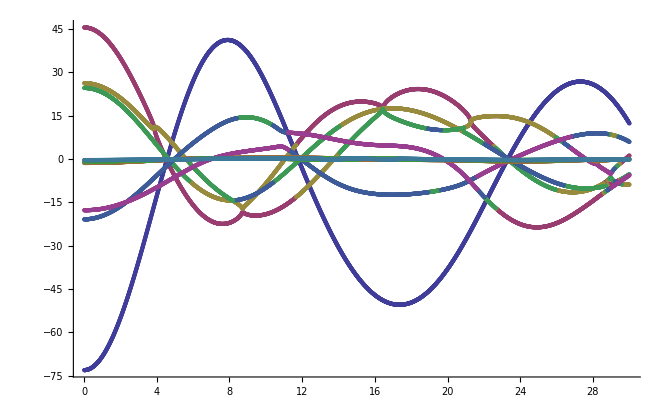

```mathematica
ListPlot[databand]
```

For the path of X--W ,  the bands are computed by inserting values of K (wave vector) in the Hamiltonian and diagonalizing for obtain the eigenenergies (bands).

```mathematica
For[ii=1, ii<sizeK+1, ii++,
vecK=Krange[[ii]]*kXW;
Bands[[ii]]=Eigenvalues[N[Hamiltonian/.Ktest->vecK,3]]]
```

We then join together the bands values for the different values of the k’s vectors. This will give us the 9 expected bands for the path in the BZ corresponding to X--W:

```mathematica
databand = ConstantArray[0,9];
For[ll=1, ll<10, ll++,databand[[ll]] = Transpose[Join[{Krange, Transpose[Re[Bands]][[ll]] }] ]]
```

Plotting the bands obtained from the calculation of the eigenenergies for the values of the wavevector Ktest:

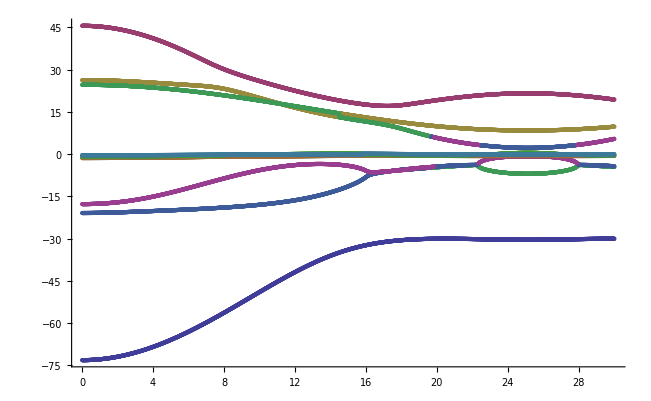

```mathematica
ListPlot[databand]
```

For the path of W--L ,  the bands are computed by inserting values of K (wave vector) in the Hamiltonian and diagonalizing for obtain the eigenenergies (bands).

```mathematica
For[ii=1, ii<sizeK+1, ii++,
vecK=Krange[[ii]]*kWL;
Bands[[ii]]=Eigenvalues[N[Hamiltonian/.Ktest->vecK,3]]]
```

We then join together the bands values for the different values of the k’s vectors. This will give us the 9 expected bands for the path in the BZ corresponding to W--L:

```mathematica
databand = ConstantArray[0,9];
For[ll=1, ll<10, ll++,databand[[ll]] = Transpose[Join[{Krange, Transpose[Re[Bands]][[ll]] }] ]]
```

Plotting the bands obtained from the calculation of the eigenenergies for the values of the wavevector Ktest:

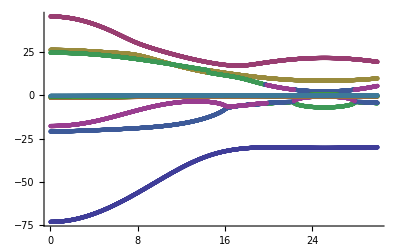

```mathematica
ListPlot[databand]
```

For the path of L--G ,  the bands are computed by inserting values of K (wave vector) in the Hamiltonian and diagonalizing for obtain the eigenenergies (bands).

```mathematica
For[ii=1, ii<sizeK+1, ii++,
vecK=Krange[[ii]]*kLG;
Bands[[ii]]=Eigenvalues[N[Hamiltonian/.Ktest->vecK,36]]]
```

We then join together the bands values for the different values of the k’s vectors. This will give us the 9 expected bands for the path in the BZ corresponding to L--G:

```mathematica
databand = ConstantArray[0,9];
For[ll=1, ll<10, ll++,databand[[ll]] = Transpose[Join[{Krange, Transpose[Re[Bands]][[ll]] }] ]]
```

Plotting the bands obtained from the calculation of the eigenenergies for the values of the wavevector Ktest:

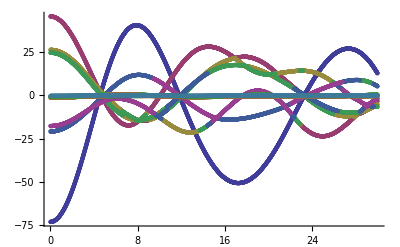

```mathematica
ListPlot[databand]
```

For the path of G--K ,  the bands are computed by inserting values of K (wave vector) in the Hamiltonian and diagonalizing for obtain the eigenenergies (bands).

```mathematica
For[ii=1, ii<sizeK+1, ii++,
vecK=Krange[[ii]]*kGK;
Bands[[ii]]=Eigenvalues[N[Hamiltonian/.Ktest->vecK,3]]]
```

We then join together the bands values for the different values of the k’s vectors. This will give us the 9 expected bands for the path in the BZ corresponding to G--K:

```mathematica
databand = ConstantArray[0,9];
For[ll=1, ll<10, ll++,databand[[ll]] = Transpose[Join[{Krange, Transpose[Re[Bands]][[ll]] }] ]]
```

Plotting the bands obtained from the calculation of the eigenenergies for the values of the wavevector Ktest:

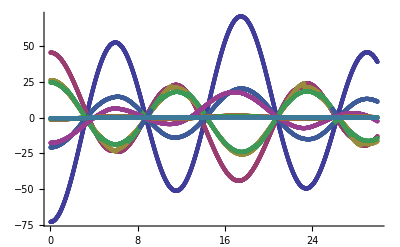

```mathematica
ListPlot[databand]
```